Kelvin Titimbo
Postdoctoral Researcher
Caltech

```mathematica
DateString[]
SetDirectory[NotebookDirectory[]]
```

Wed 26 Nov 2025 11:31:47

D:\titimbo\SingleSG_Xukun2025

```mathematica
σ[y_]=1/(1+ⅇ^-y);
windowSigmoid[y_,y1_,y2_,win_,wout_]:=σ[(y-y1)/win]*(1-σ[(y-y2)/wout]);
```

```mathematica
GProfile[y_,y1_,y2_,win_,wout_]:=Module[{ygrid,wvals,norm},
ygrid=Subdivide[1/2 y1,2*y2,1000];
wvals=windowSigmoid[#,y1,y2,win,wout]&/@ygrid;
norm=Max[wvals];
windowSigmoid[y,y1,y2,win,wout]/norm]
```

```mathematica
yin = 26.8;
yout=33.8;
win=0.1;
wout=0.1;
```

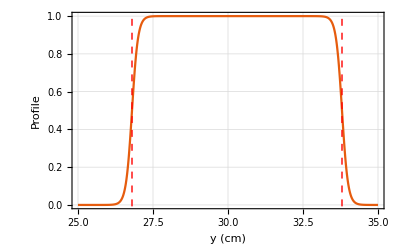

```mathematica
Plot[GProfile[y,yin,yout,win,wout],{y,25.0,35.0},
PlotRange->All,
AxesLabel->{"z (m)","G(z)"},
PlotTheme->"Scientific",
FrameLabel->{"y (cm)","Profile"},
GridLines->Automatic,
Epilog->{{Red,Thick,Dashed,Line[{{zin,-10^6},{zin,10^6}}]},{Red,Thick,Dashed,Line[{{zout,-10^6},{zout,10^6}}]}}
]
```

```mathematica
G[y_]:=GProfile[y,zin,zout,win,wout];
```

```mathematica
fieldvscurrent= Import["SG_BvsI.csv"];
gradientvscurrent={{0,0},{0.095,25.6},{0.2,58.4},{0.302,92.9},{0.405,132.2},{0.498,164.2},{0.6,196.3},{0.7,226},{0.75,240},{0.8,253.7},{0.902,277.2},{1.01,298.6}};
```

```mathematica
gvsI=Interpolation[gradientvscurrent];
BvsI=Interpolation[fieldvscurrent];
```

```mathematica
(*Acceleration scale (set to whatever you need)*)
a0=1.0;         (*units:whatever your z-units/t-units imply*)
z0=0.0;         (*initial position*)
vz0=0.0;         (*initial velocity*)

tmax=1.0;        (*total integration time*)

eqns={z''[t]==a0*G[z[t]],z[0]==z0,z'[0]==vz0};

sol=NDSolve[eqns,z,{t,0,tmax},Method->{"StiffnessSwitching"} (*usually robust*)];
```

FittedModel[…]

0.998589 |  | Estimate | Standard Error | t-Statistic | P-Value
a | 309.706 | 7.23761 | 42.7912 | 1.16603×10^-12
b | 2.14324 | 4.40171 | 0.486912 | 0.636817

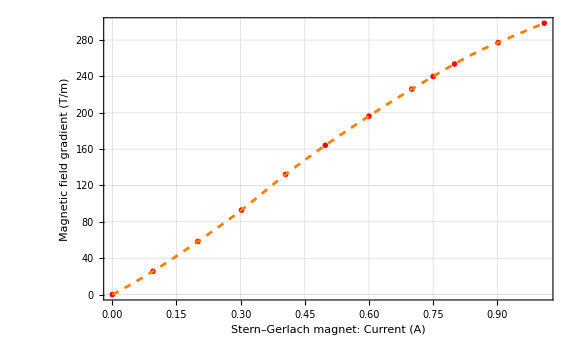

```mathematica
fitgradvsI=NonlinearModelFit[gradientvscurrent,a x+b,{a,b},x]
TableForm[{{fitgradvsI["RSquared"],fitgradvsI["ParameterTable"]}}]

dBdzvsI=Interpolation[gradientvscurrent];
Show[ListPlot[gradientvscurrent,
Frame->True,FrameStyle->Directive[Black,Thickness[0.002]],FrameLabel->{Style["Stern–Gerlach magnet: Current (A)",Bold,12],Style["Magnetic field gradient (T/m)",Bold,12]},LabelStyle->Directive[12],GridLines->Automatic,GridLinesStyle->Directive[LightGray,Thickness[0.001]],PlotStyle->Red,PlotMarkers->{"OpenMarkers",5}],
Plot[dBdzvsI[x],{x,0,1},PlotStyle->Directive[Orange,Dashed]],
ImageSize->Large
]
```

```mathematica
function μF_effective(Ix,F,mF,p::AtomParams)
# Promote to Float64 to avoid mixed-type arithmetic issues
II=float(p.Ispin)
γₙ=p.γn

Ix,F,mF=promote(float(Ix),float(F),float(mF))

# Energy scale and adimensional field
ΔE=2π*ħ*p.Ahfs*(II+1/2)
normalized_B=(γₑ-γₙ)*ħ/ΔE*BvsI(Ix)

# Validate quantum numbers
is_F_upper=isapprox(F,II+0.5;atol=1e-12)
is_F_lower=isapprox(F,II-0.5;atol=1e-12)
if!(is_F_upper||is_F_lower)
throw(ArgumentError("F must be I±1/2; got F=$F for I=$II"))
end
if mF<-F-1e-12||mF>F+1e-12
throw(ArgumentError("mF must be in [-F, F]; got mF=$mF for F=$F"))
end

# Common pieces
ratio=γₙ/γₑ
denom_arg=1-4*mF/(2*II+1)*normalized_B+normalized_B^2
# Clamp tiny negative due to rounding
denom=sqrt(max(denom_arg,0.0))

μF::Float64=NaN #<--initialize
if is_F_upper
if isapprox(mF,F;atol=1e-12)||isapprox(mF,-F;atol=1e-12)
s=sign(mF)
μF=s*(gₑ/2)*(1+2*ratio*II)*μB
else
μF=gₑ*μB*(mF*ratio+(1-ratio)/denom*(mF/(2*II+1)-0.5*normalized_B))
end
else # is_F_lower
μF=gₑ*μB*(mF*ratio-(1-ratio)/denom*(mF/(2*II+1)-0.5*normalized_B))
end

return Float64(μF)
end
```

```mathematica
1/(2π 2.25 10^-6)
```

70735.5